# Analysis of fitness dynamics

## This doesn’t use the scaffolded variant fitnesses relative to wildtype and instead directly looks at change of mean population fitness

```mathematica
virus="h3n2"; (*"sarscov2", "h3n2"*)
```

```mathematica
classification="clades"; (*"clades", "lineages"*)
```

## Setup

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/trvrb/Documents/src/fitness-dynamics/fitness-flux-analysis

```mathematica
virusToDisplayName={"sarscov2"->"SARS-CoV-2","h3n2"->"H3N2"};
```

```mathematica
virusToMutationDisplayName={"sarscov2"->"S1","h3n2"->"HA1"};
```

```mathematica
classificationToDisplayName={"clades"->"Clade","lineages"->"Lineage"};
```

```mathematica
availableDatasets=Map[Last[StringSplit[#,"/"]]&,FileNames[All,"../mlr-estimates/"]]
```

{.DS_Store,h3n2_clades_2016-17,h3n2_clades_2017-18,h3n2_clades_2018-19,h3n2_clades_2019-20,h3n2_clades_2020-21,h3n2_clades_2021-22,h3n2_clades_2022-23,h3n2_clades_2023-24,sarscov2_clades_2020,sarscov2_clades_2020-21,sarscov2_clades_2021,sarscov2_clades_2021-22,sarscov2_clades_2022,sarscov2_clades_2022-23,sarscov2_clades_2023,sarscov2_clades_2023-24,sarscov2_clades_2024,sarscov2_lineages_2020,sarscov2_lineages_2020-21,sarscov2_lineages_2021,sarscov2_lineages_2021-22,sarscov2_lineages_2022,sarscov2_lineages_2022-23,sarscov2_lineages_2023,sarscov2_lineages_2023-24,sarscov2_lineages_2024}

```mathematica
timepoints=Cases[Map[StringSplit[#,"_"]&,availableDatasets],x_/;x[[1]]==virus&&x[[2]]==classification][[All,3]]
```

{2016-17,2017-18,2018-19,2019-20,2020-21,2021-22,2022-23,2023-24}

```mathematica
timepoints=DeleteCases[timepoints,"2020-24"]
```

{2016-17,2017-18,2018-19,2019-20,2020-21,2021-22,2022-23,2023-24}

```mathematica
virusToVariantLabels={"sarscov2"->{"19B"->"WT","20A"->"D614G","20I"->"Alpha","21J"->"Delta","21K"->"Omicron BA.1","21L"->"BA.2","22B"->"BA.5","22E"->"BQ.1","23A"->"XBB.1.5","23F"->"EG.5.1","24A"->"JN.1","24E"->"KP.3.1.1"},"h3n2"->{"B.2"->"B.2","G.1.1"->"G.1.1","J"->"J","J.2"->"J.2"}};
```

Generation time in years

```mathematica
generationTime=3.2/365.
```

0.00876712

```mathematica
col=ColorData["Rainbow"][0.3]
```

RGBColor[0.2979596, 0.5657928, 0.7522386000000001]

## Functions

### Colors

```mathematica
start[n_]:=0.07;
```

```mathematica
stop[n_]:=0.99;
```

```mathematica
gap[n_]:=(stop[n]-start[n])/(n-1)
```

```mathematica
makeColors[n_]:=Table[ColorData["Rainbow"][i],{i,start[n],stop[n],gap[n]}];
```

```mathematica
startGrays[n_]:=0.35;
```

```mathematica
stopGrays[n_]:=0.65;
```

```mathematica
gapGrays[n_]:=(stopGrays[n]-startGrays[n])/(n-1)
```

```mathematica
makeGrays[n_]:=Table[GrayLevel[i],{i,startGrays[n],stopGrays[n],gapGrays[n]}];
```

### Other

```mathematica
gappedPartition[list_,n_]:=Partition[list,n,n,1,""]
```

```mathematica
timepointToNumeric[timepoint_]:=N[Mean[Map[If[ToExpression[#]>2000,ToExpression[#],ToExpression[#]+2000]&,StringSplit[timepoint,"-"]]]]
```

### Comparing date series

```mathematica
compareSeries[dateSeries1_,dateSeries2_,dates_]:=Map[{#[[1,2]],#[[2,2]]}&,DeleteCases[Map[{FirstCase[dateSeries1,x_/;x[[1]]==#],FirstCase[dateSeries2,x_/;x[[1]]==#]}&,dates],{x_,y_}/;x==Missing["NotFound"]||y==Missing["NotFound"]]]
```

```mathematica
correlateSeries[dateSeries1_,dateSeries2_,dates_]:=Apply[Correlation,N[Transpose[compareSeries[dateSeries1,dateSeries2,dates]]]]
```

## Gather timepoint specific fitnesses

```mathematica
logVariantFitnessesForTimePoint[timepoint_]:=Module[{jsonData,variants,dates,elements,variantToFitness},
jsonData=Import["../mlr-estimates/"<>virus<>"_"<>classification<>"_"<>timepoint<>"/mlr_results.json"];
variants="variants"/.("metadata"/.jsonData);
dates="dates"/.("metadata"/.jsonData);
elements="data"/.jsonData;
elements=DeleteCases[elements,x_/;("value"/.x)==Null];
variantToFitness=Table[With[{elems=Cases[elements,x_/;("site"/.x)=="ga"&&("ps"/.x)=="median"&&("location"/.x)=="USA"&&("variant"/.x)==variant]},
variant->If[Length[elems]>0,("value"/.elems)[[1]],1]],{variant,variants}];
Map[#[[1]]->Log[#[[2]]]&,variantToFitness]
]
```

```mathematica
logVariantFitnessesForTimePoint["2022-23"]
```

{G.1→-0.0429075,G.1.1→-0.0212236,G.1.1.1→-0.109815,G.1.1.2→0.0198026,G.1.3→-0.0512933,G.1.3.2→-0.040822,G.2.1→0.0198026,G.2.2→0.0129162,J→0.0295588,J.1→0.079735,J.2→0.0962189,J.2.d→0.162969,other→-0.0120726,G.2→0}

## Gather timepoint specific frequencies

```mathematica
variantRawFrequenciesForTimePoint[timepoint_]:=Module[{jsonData,variants,dates,elements,variantToRawFrequencies},
jsonData=Import["../mlr-estimates/"<>virus<>"_"<>classification<>"_"<>timepoint<>"/mlr_results.json"];
variants="variants"/.("metadata"/.jsonData);
dates="dates"/.("metadata"/.jsonData);
elements="data"/.jsonData;
elements=DeleteCases[elements,x_/;("value"/.x)==Null];
variantToRawFrequencies=Table[With[{elems=Cases[elements,x_/;("site"/.x)=="weekly_raw_freq"&&("location"/.x)=="USA"&&("variant"/.x)==variant]},
variant->Map[{"date"/.#,"value"/.#}&,elems]],{variant,variants}];
variantToRawFrequencies
]
```

## Daily mean fitness per timepoint

This is just a weighted average of variant fitness × variant frequency
This is the center of the traveling wave

```mathematica
logMeanFitnessForTimepoint[timepoint_]:=Module[{logFitnesses,variants,frequencies,dates},
logFitnesses=logVariantFitnessesForTimePoint[timepoint];
variants=logFitnesses[[All,1]];
frequencies=variantRawFrequenciesForTimePoint[timepoint];
dates=frequencies[[1,2,All,1]];
Transpose[{dates,Sum[(variant/.logFitnesses)*(variant/.frequencies)[[All,2]],{variant,variants}]}]
]
```

## Fitness flux per timepoint

Calculate change in log mean fitness over +30 day windows

```mathematica
velocityWindow=30
```

30

```mathematica
logFitnessVelocities=Table[With[{time=QuantityMagnitude[DateDifference[dates[[i-velocityWindow]],dates[[i]],"Years"]],distance=logMeanFitnesses[[i,2]]-logMeanFitnesses[[i-velocityWindow,2]]},{dates[[i-(velocityWindow/2)]],(distance/time)}],{i,velocityWindow+1,Length[dates]}];
```

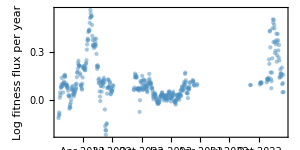

```mathematica
figVelocity=DateListPlot[Map[{#[[1]],#[[2]]}&,logFitnessVelocities],PlotTheme->"FullAxes",Joined->False,Frame->{True,True,False,False},FrameLabel->{"","Log fitness flux per year"},PlotRange->All,PlotStyle->Directive[col,AbsolutePointSize[3],Opacity[0.5]],ImageSize->300,AspectRatio->0.5,ImagePadding->{{60,7},{15,10}}]
```

## Cumulative fitness flux

```mathematica
cumulativeFitnessFluxForTimepoint[timepoint_]:=Module[{logMeanFitnesses,initialLogFitness},
logMeanFitnesses=logMeanFitnessForTimepoint[timepoint];
initialLogFitness=logMeanFitnesses[[1,2]];
Map[{#[[1]],#[[2]]-initialLogFitness}&,logMeanFitnesses]
]
```

```mathematica
series=Table[cumulativeFitnessFluxForTimepoint[timepoint],{timepoint,timepoints}];
```

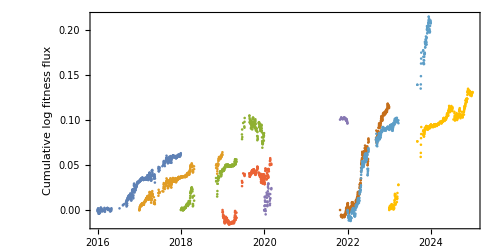

```mathematica
DateListPlot[series,PlotTheme->"FullAxes",Joined->False,Frame->{True,True,False,False},FrameLabel->{"","Cumulative log fitness flux"},PlotRange->All,ImageSize->500,AspectRatio->0.5,ImagePadding->{{60,7},{15,10}}]
```